-Graphics-

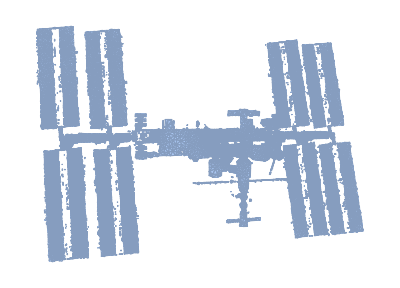

-Graphics3D-

-Graphics-

-Graphics3D-

```mathematica
imgs={-Graphics-,-Graphics-,-Graphics-};
mask=Erosion[Binarize[imgs[[2]],0],1];
parallaxL=First@ImageDisplacements[imgs[[{2,1}]]];
parallaxR=First@ImageDisplacements[imgs[[{2,3}]]];
parallax=parallaxL-parallaxR;
depth=Blur@Opening[ImageMultiply[ImageAdjust@Image[parallax[[All,All,1]]],mask],DiskMatrix[4]]
depthFunction=ListInterpolation[Transpose@Reverse@ImageData[depth]];
resolution=ImageAdjust@ImageSaliencyFilter[imgs[[2]]];
resolutionFunction=ListInterpolation[Transpose@Reverse@ImageData@resolution];
Ω=TriangulateMesh[ImageMesh[Erosion[mask,DiskMatrix[2]]],MeshRefinementFunction->Function[{vertices,area},area>32+512 (1-resolutionFunction@@Mean[vertices])^6]]
Graphics3D[GraphicsComplex[Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],{EdgeForm[],MeshCells[Ω,2]}],PlotRange->Append[Thread[{0,ImageDimensions[mask]}],{0,1}],BoxRatios->{1,1,2/3},ViewPoint->Top]
texture=SetAlphaChannel[imgs[[2]],mask]
Graphics3D[{Texture[texture],GraphicsComplex[Apply[{##,depthFunction[##]}&,MeshCoordinates[Ω],{1}],{EdgeForm[],MeshCells[Ω,2]},VertexTextureCoordinates->Map[#/ImageDimensions[texture]&,MeshCoordinates[Ω]]]},PlotRange->Append[Thread[{0,ImageDimensions[mask]}],{0,1}],BoxRatios->{1,1,2/3},Lighting->{{"Ambient",White}},ViewPoint->Top,Boxed->False]
```